# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pcs/Desktop/LMG

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,Sy,F];

Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
(*SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];*)
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);

Clear[F];
F[J_,α_,k_,τ_]:=MatrixExp[N[(-I*k/(2J))(Sx[J].Sx[J])]].MatrixExp[(-I*α*τ)(Sz[J])];

Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

# Method

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],20]]
];
Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],20]]
];
```

```mathematica
radius=1.99999;
delta=0.04;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

8030

```mathematica
radius=0.6;
delta=0.01;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
region=gridPoints;
region//Length
```

14641

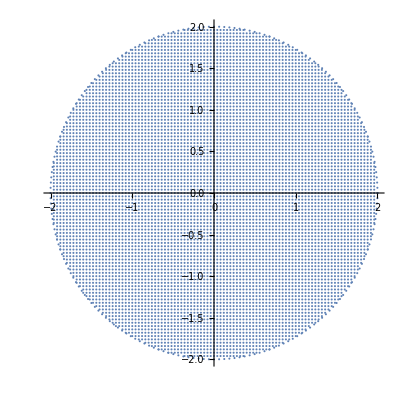

```mathematica
ListPlot[region,AspectRatio->1]
```

## LMG

```mathematica
Clear[Hlmg, floq];
Hlmg[J_]:=Hlmg[J]=N[(gy/(2J-1))(Sy[J].Sy[J])+(gx/(2J-1))(Sx[J].Sx[J])+(Sz[J])];
```

```mathematica
Clear[gx,gy];
gx=-0.5;
gy=-3.;
```

```mathematica
Clear[lipmatm,lipmatM];
J=300;
mat2=Hlmg[J];
(*mat2=ConjugateTranspose[rotation].Hlmg[J].rotation;*)
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];
```

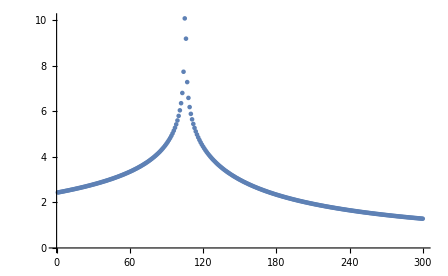

```mathematica
ListPlot[(2Pi)/Differences[Chop[lipeigenvalM]],PlotRange->All]
(*ListPlot[(2Pi)/Differences[Chop[lipeigenvalm]],PlotRange->All]*)
```

## Husimis

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Quiet[Abs[Conjugate[cohes[[i]]].ψ]^2]},{i,Length[region]}];
```

```mathematica
plots={};
Do[
mat2=Hlmg[J];
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
(*lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];*)
inieigen=Normalize[Conjugate[lipneweigenvec].a2[J,0,0]];
data=SortBy[Transpose[{Abs[inieigen]^2,lipneweigenvec}],First];
AppendTo[plots,ParallelTable[Total[Quiet[Abs[data[[All,2]][[i]]]^4]],{i,-1,-5,-1},DistributedContexts->Full]];
,{J,50,500,50}];
```

```mathematica
jlist=Range[50,500];
newdata=Table[{Log[2*jlist[[i]]+1],Log[plots[[i,j]]]},{j,5},{i,Length[plots]}];
```

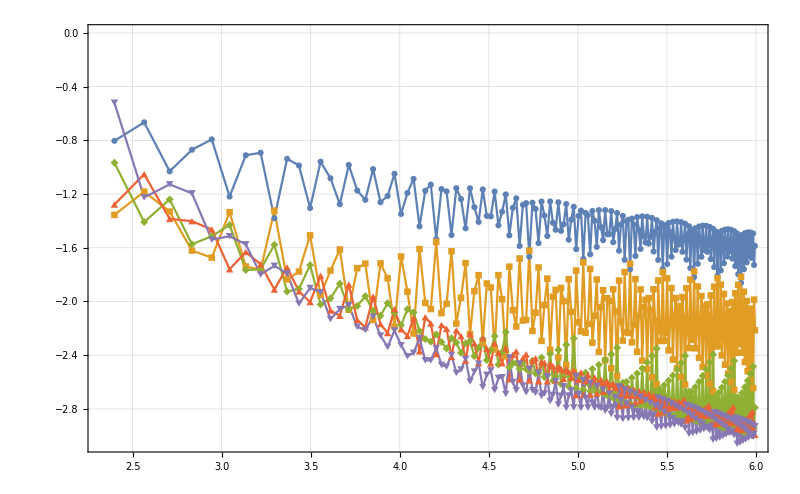

```mathematica
ListPlot[newdata,PlotRange->All,ImageSize->800,PlotTheme->"Detailed",Joined->True,PlotMarkers->Automatic]
```

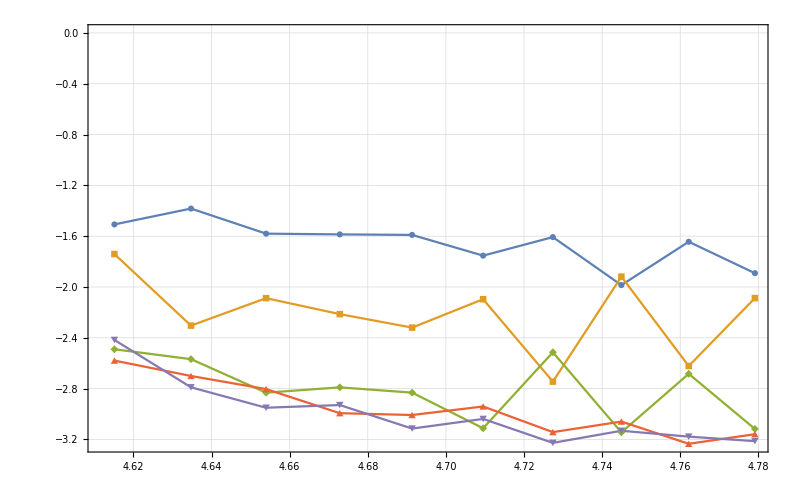

```mathematica
ListPlot[newdata,PlotRange->All,ImageSize->800,PlotTheme->"Detailed",Joined->True,PlotMarkers->Automatic]
```

```mathematica
ListAnimate[Table[ListPlot[newdata[[j]],PlotRange->All,ImageSize->800,PlotTheme->"Detailed",Joined->True,PlotMarkers->Automatic],{j,5}],AnimationRunning->False]
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region},DistributedContexts->Full];
```

```mathematica
data=SortBy[Transpose[{lipneweigenval,lipneweigenvec}],First];
```

```mathematica
Do[

Export["Eigenvec_"<>ToString[i]<>"_J_"<>ToString[J]<>", dq_"<>ToString[delta]<>".png",ListDensityPlot[husimi[data[[i]][[2]]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["Eigenvec +"<>ToString[i]<>", J = "<>ToString[J]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,2J+1}]
```

$Aborted

## Scaling

```mathematica
jlist=Range[50,500];
```

```mathematica
data={};
Do[

mat2=Hlmg[J];
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];
cohelist=Table[ini=a2[J,Q,0],{Q,-2/10,19/10,1/10}];
ipr=ParallelTable[Total[Quiet[Abs[Conjugate[lipneweigenvec].i]^4]],{i,cohelist},DistributedContexts->Full];
AppendTo[data,{J,ipr}];

,{J,jlist}];
```

$Aborted

```mathematica
Transpose[data[[All,2]]]//Dimensions
```

{22,372}

```mathematica
ListAnimate[Table[ListPlot[Log[Transpose[{data[[All,1]],Transpose[data[[All,2]]][[i]]}]],PlotRange->All,PlotTheme->"Detailed",ImageSize->800,Joined->True,PlotMarkers->Automatic],{i,22}],AnimationRunning->False]
```